Set::write: -(3 (-2 ξ (Cos[Times[«2»]] Cosh[Times[«2»]]+Cos[Times[«2»]] Cosh[Times[«2»]])-Cosh[(1+d) ξ] Sin[(-1+d) ξ]+Cosh[(1+Times[«2»]) ξ] Sin[(1+d) ξ]+Cos[(1+d) ξ] Sinh[(1+Times[«2»]) ξ]+Cos[(-1+d) ξ] Sinh[(1+d) ξ]))/(4 ξ^3 (Cos[2 d ξ]+Cosh[2 d ξ]))/.3/4 Abs[(-2 ξ (Times[«2»]+Times[«2»])-Cosh[Times[«2»]] Sin[Times[«2»]]+Cosh[Times[«2»]] Sin[Times[«2»]]-Cos[Times[«2»]] Sinh[Times[«2»]]+Cos[Times[«2»]] Sinh[Times[«2»]])/(ξ^3 (Cos[Times[«2»]]+Cosh[Times[«2»]]))]のタグReplaceAllはProtectedです．

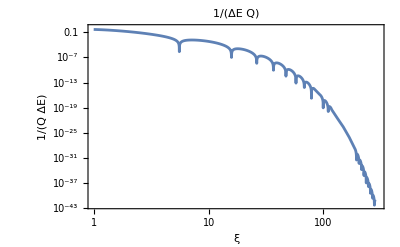

```mathematica
f=3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))/.
QHeatFlow=Abs[f]/.
{d->1.3};
QHeatFlowg=LogLogPlot[QHeatFlow,{ξ,1,300},PlotLabel->Q^-1/ΔE, Frame->True,FrameLabel->{ξ,Q^-1/ΔE}]
```

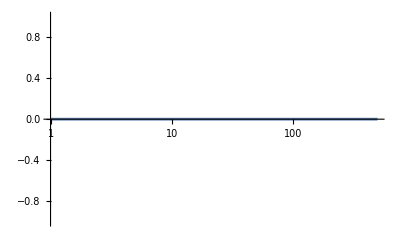

```mathematica
Qd=D[f,ξ]/.
Solve[Qd==0,ξ]/.
{d->1.3};
LogLinearPlot[Qd,{ξ,1,500}]
```

```mathematica
Solve[D[f,ξ]==0,ξ]
```

{{}}

```mathematica
FindMinimum[QHeatFlow,ξ]
```

FindMinimum::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

{1.09151×10^-10,{ξ→5.5641}}

```mathematica
FindArgMin[QHeatFlow,{ξ,3,100}]
```

{5.5641}

```mathematica
FindMinimum[QHeatFlow,{ξ,5,100}]
```

{1.79124×10^-9,{ξ→15.8166}}

```mathematica
FindArgMin[QHeatFlow,{ξ,20,100}]
```

{26.246}

```mathematica
FindArgMin[QHeatFlow,{ξ,30,100}]
```

{36.502}

```mathematica
FindArgMin[QHeatFlow,{ξ,40,50}]
```

{47.8116}

```mathematica
FindArgMin[QHeatFlow,{ξ,50,100}]
```

General::ovfl: 計算中にオーバーフローが起りました．

General::stop: この計算中に，General::ovflのこれ以上の出力は表示されません．

FindArgMin::nrnum: 関数の値Overflow[]は{ξ} = {1.89594×10^15}において実数ではありません．

FindArgMin[QHeatFlow,{ξ,50,100}]

```mathematica
FindArgMin[QHeatFlow,ξ∈{20,100}]
```

FindArgMin::lstol: 直線探索において刻み幅をAccuracyGoalとPrecisionGoalで指定された許容範囲内に減らしましたが，関数に十分な減少が見られませんでした．これらの許容範囲で満足するためには，MachinePrecision桁より高い作業精度が必要となることがあります．

{5.5641}